# Cálculo da Impedância Característica e potência natural de diversos circuitos de transmissão

## Antonio Carlos S Lima EEE457 - Transmissão de Energia Elétrica 2021/2

## Início

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\anton\Dropbox\UFRJ\cursos\EEE457-Transmissão_Energia_Elétrica\arquivos_Mma_EEE457

### Algumas constantes

```mathematica
μ= 4.0 π 10^-7;
ϵ= 8.854 10^-12;
σs=10.0^-3;
ℓ=80 10^3; (* comprimento do circuito *)
```

cabos pararraios possuem permeabilidade magnética relativa próximo a 100

```mathematica
μr= 90.0;
```

```mathematica
Sb= 100.0;
```

## circuito 500 kV

3x Rail

```mathematica
Vb= 500.;
z1= 0.0272+I 0.3209;
y1= I 5.1462 10^-6;
Zc1= Sqrt[z1/y1]
```

249.937-10.5736 ⅈ

```mathematica
P1= Vb^2/Zc1
```

998.465+42.24 ⅈ

4x Rail

### Cáculo dos quadripolos

```mathematica
qm[z_,y_,ℓ_]:={{1+ z ℓ y ℓ/2, z ℓ},{y ℓ/2 (1+ z ℓ y ℓ/4), 1+ z ℓ y ℓ/2}}
```

```mathematica
ql[z_,y_,ℓ_]:=With[{zc=Sqrt[z/y], γ=Sqrt[z y]},{{Cosh[γ ℓ], zc Sinh[γ ℓ]},{1/zc Sinh[γ ℓ], Cosh[γ ℓ]}}]
```

```mathematica
vr= 500. 10^3/Sqrt[3];
ir =vr/ Zc1
```

1152.93+48.7746 ⅈ

```mathematica
quad1=qm[z1, y1, 220];
```

```mathematica
quad1[[1,1]]
```

0.960036+0.00338743 ⅈ

```mathematica
1/quad1[[1,1]]
```

1.04161-0.00367528 ⅈ

```mathematica
quad2=ql[z1,y1,220.0];
```

```mathematica
1/quad2[[1,1]]
```

1.04133-0.00362453 ⅈ

```mathematica
{vs, is} =quad1.{vr, ir};
```

```mathematica
Abs[vs]Sqrt[3]
```

506655.

```mathematica
Abs[is]
```

1126.33

```mathematica
am[z_,y_, ℓ_]:=1+ z ℓ y ℓ/2
al[z_,y_, ℓ_]:=Cosh[Sqrt[z y]ℓ]
bm[z_,y_, ℓ_]:= z ℓ 
bl[z_,y_, ℓ_]:=Sqrt[z/y]Sinh[Sqrt[z y]ℓ]
```

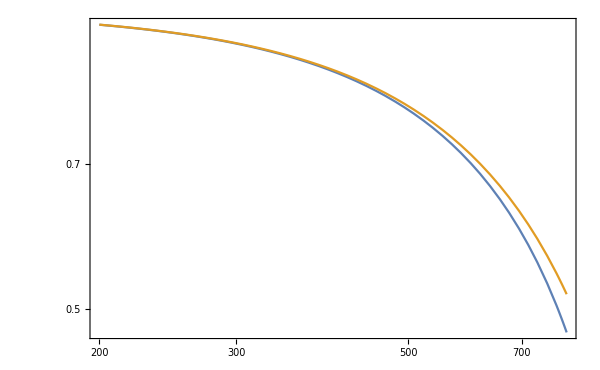

```mathematica
LogLogPlot[{Abs[am[z1,y1,x]],Abs[al[z1,y1,x]]},{x, 200, 800}, PlotRange->All,BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,
Axes-> False,Frame-> True,PlotRange->All]
```

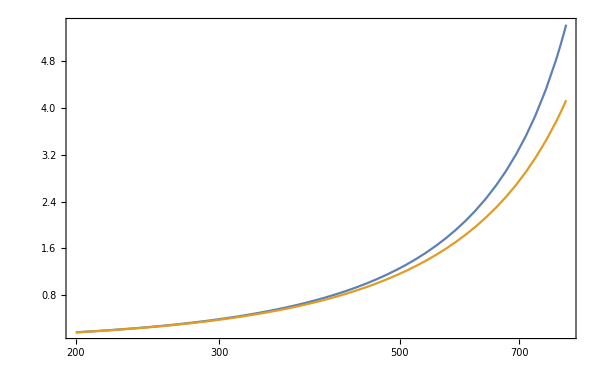

```mathematica
LogLinearPlot[{180/π Arg[am[z1,y1,x]],180/π Arg[al[z1,y1,x]]},{x, 200, 800}, PlotRange->All,BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,
Axes-> False,Frame-> True,PlotRange->All]
```

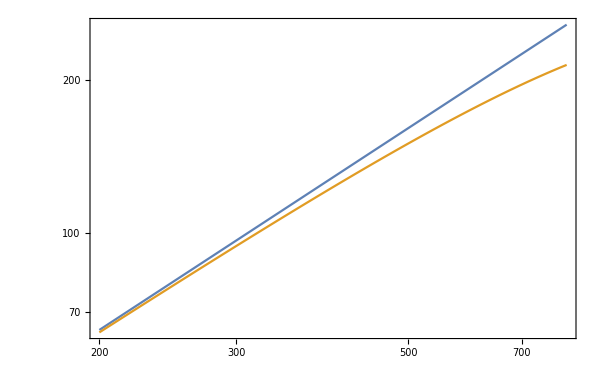

```mathematica
LogLogPlot[{Abs[bm[z1,y1,x]],Abs[bl[z1,y1,x]]},{x, 200, 800}, PlotRange->All,BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,
Axes-> False,Frame-> True,PlotRange->All]
```

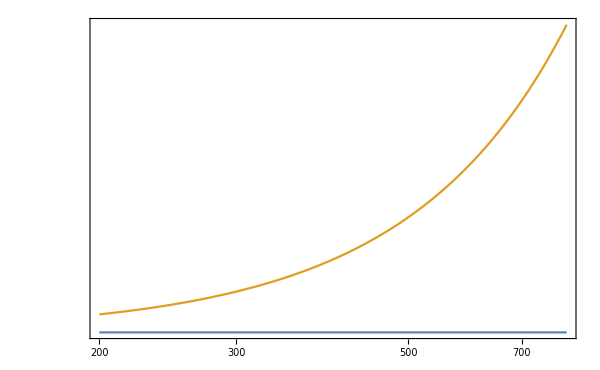

```mathematica
LogLogPlot[{Arg[bm[z1,y1,x]],Arg[bl[z1,y1,x]]},{x, 200, 800}, PlotRange->All,BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,
Axes-> False,Frame-> True,PlotRange->All]
```